```mathematica
Quit[]
```

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m"
```

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

```mathematica
Remove[q1]
Remove[q2]
<<"/home/riccardo/Programs/ABISS/ABISS.m"
```

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

ABISS: A link to the model file SMbgf_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general_backup.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general+SM.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgfQCD_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_TelescopeOctopus_backup.mod has been added to the FeynArts directory

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Tesi/EWProcesses/GFindependence/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Tesi/EWProcesses/GFindependence/input/integral_families.m already exist. It will NOT be overwritten.

Import the input files (kinematics + integral families).

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/GFindependence/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/GFindependence/input/kinematics.m.

```mathematica
userIntegralMasses[userIntegralFamiliesNames]
```

userIntegralMasses[{A0,B0,C0,D0}]

## Diagrams generation

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish_var", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing}, ExcludeParticles-> {}];
```

```mathematica
process={F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]};
```

```mathematica
topologiesBorn=CreateTopologies[0,2->2,ExcludeTopologies->Tadpoles];
```

```mathematica
fieldsBorn=InsertFields[topologiesBorn, process];
fieldsZ=DiagramSelect[fieldsBorn,!FreeQ[#,Field[5]->V[20]]&];
fieldsG=DiagramSelect[fieldsBorn,!FreeQ[#,Field[5]->S[20]]&];
fieldsGa=DiagramSelect[fieldsBorn,!FreeQ[#,Field[5]->V[10]]&];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish_var.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf_Anglerfish_var} initialized

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 4 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 24 field point(s)

in total: 4 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

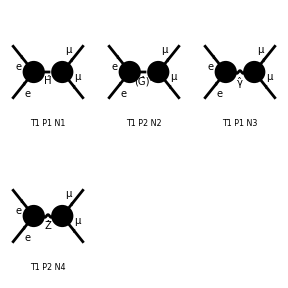

```mathematica
Paint[fieldsBorn];
```

```mathematica
ampZ=CreateFeynAmp[fieldsZ, GaugeRules->{}];
ampG=CreateFeynAmp[fieldsG, GaugeRules->{}];
ampGa=CreateFeynAmp[fieldsGa, GaugeRules->{}];
ampBorn=CreateFeynAmp[fieldsBorn, GaugeRules->{}];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

in total: 4 Particles amplitudes

```mathematica
myAmpZ=ExtractAmplitude[ampZ];
myAmpG=ExtractAmplitude[ampG];
myAmpGa=ExtractAmplitude[ampGa];
myAmpBorn=ExtractAmplitude[ampBorn]; (*"Extracts from a FeynArts amplitude a list of amplitudes in the format understood by ABISS."*)
```

```mathematica
SaveAmplitudes[myAmpZ,"ZAmplitudes.m"];
SaveAmplitudes[myAmpG,"GAmplitudes.m"];
SaveAmplitudes[myAmpGa,"GaAmplitudes.m"];
SaveAmplitudes[myAmpG,"BornAmplitudes.m"];
```

ABISS: Amplitudes saved in /home/riccardo/Documents/Tesi/EWProcesses/GFindependence/feynArts_amplitudes/ZAmplitudes.m

ABISS: Amplitudes saved in /home/riccardo/Documents/Tesi/EWProcesses/GFindependence/feynArts_amplitudes/GAmplitudes.m

ABISS: Amplitudes saved in /home/riccardo/Documents/Tesi/EWProcesses/GFindependence/feynArts_amplitudes/GaAmplitudes.m

ABISS: Amplitudes saved in /home/riccardo/Documents/Tesi/EWProcesses/GFindependence/feynArts_amplitudes/BornAmplitudes.m

## Interference

```mathematica
ImportInput[]
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/GFindependence/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/GFindependence/input/kinematics.m.

### Lagrangian parameter replace

```mathematica
<<(NotebookDirectory[]<>"smparameters.m")
parameterReplace=smparameters;
```

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,0,1,0],userIntegral[A0,{mh,mm},1,1,1,-1],userIntegral[A0,{mh,mm},1,-1,1,0],userIntegral[A0,{mh,mm},1,0,1,-1],userIntegral[A0,{mh,mm},1,1,1,-2],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mh,mm},1,1,0,-1],userIntegral[A0,{mh,mm},1,1,-1,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,0,1,0],userIntegral[A0,{mh,mm},0,1,1,-1],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},-1,1,1,0],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[A0,{mz,mm},1,0,1,0],userIntegral[A0,{mz,mm},1,1,1,-1],userIntegral[A0,{mz,mm},1,-1,1,0],userIntegral[A0,{mz,mm},1,0,1,-1],userIntegral[A0,{mz,mm},1,1,1,-2],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,0,-1],userIntegral[A0,{mz,mm},1,1,-1,0],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},0,0,1,0],userIntegral[A0,{mz,mm},0,1,1,-1],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},-1,1,1,0],userIntegral[C0,{mw},1,1,1,0],userIntegral[C0,{mw},1,0,1,0],userIntegral[C0,{mw},1,1,1,-1],userIntegral[C0,{mw},1,-1,1,0],userIntegral[C0,{mw},1,0,1,-1],userIntegral[C0,{mw},1,1,1,-2],userIntegral[C0,{mw},1,1,0,0],userIntegral[C0,{mw},1,0,0,0],userIntegral[C0,{mw},1,1,0,-1],userIntegral[C0,{mw},1,1,-1,0],userIntegral[C0,{mw},0,1,1,0],userIntegral[C0,{mw},0,0,1,0],userIntegral[C0,{mw},0,1,1,-1],userIntegral[C0,{mw},0,1,0,0],userIntegral[C0,{mw},-1,1,1,0],userIntegral[D0,{mm,mh,mz},1,0,1,0],userIntegral[D0,{mm,mh,mz},1,1,1,-1],userIntegral[D0,{mm,mh,mz},1,1,1,0],userIntegral[D0,{mm,mh,mz},1,-1,1,0],userIntegral[D0,{mm,mh,mz},1,0,1,-1],userIntegral[D0,{mm,mh,mz},1,1,1,-2],userIntegral[D0,{mm,mh,mz},1,1,0,0],userIntegral[D0,{mm,mh,mz},1,0,0,0],userIntegral[D0,{mm,mh,mz},1,1,0,-1],userIntegral[D0,{mm,mh,mz},1,1,-1,0],userIntegral[D0,{mm,mh,mz},0,1,1,0],userIntegral[D0,{mm,mh,mz},0,0,1,0],userIntegral[D0,{mm,mh,mz},0,1,1,-1],userIntegral[D0,{mm,mh,mz},0,1,0,0],userIntegral[D0,{mm,mh,mz},-1,1,1,0],userIntegral[D0,{mm,mz,mh},1,0,1,0],userIntegral[D0,{mm,mz,mh},1,1,1,-1],userIntegral[D0,{mm,mz,mh},1,1,1,0],userIntegral[D0,{mm,mz,mh},1,-1,1,0],userIntegral[D0,{mm,mz,mh},1,0,1,-1],userIntegral[D0,{mm,mz,mh},1,1,1,-2],userIntegral[D0,{mm,mz,mh},1,1,0,0],userIntegral[D0,{mm,mz,mh},1,0,0,0],userIntegral[D0,{mm,mz,mh},1,1,0,-1],userIntegral[D0,{mm,mz,mh},1,1,-1,0],userIntegral[D0,{mm,mz,mh},0,1,1,0],userIntegral[D0,{mm,mz,mh},0,0,1,0],userIntegral[D0,{mm,mz,mh},0,1,1,-1],userIntegral[D0,{mm,mz,mh},0,1,0,0],userIntegral[D0,{mm,mz,mh},-1,1,1,0],userIntegral[B0,{mw},1,0,1,0],userIntegral[B0,{mw},1,1,1,-1],userIntegral[B0,{mw},1,1,1,0],userIntegral[B0,{mw},1,-1,1,0],userIntegral[B0,{mw},1,0,1,-1],userIntegral[B0,{mw},1,1,1,-2],userIntegral[B0,{mw},1,1,0,0],userIntegral[B0,{mw},1,0,0,0],userIntegral[B0,{mw},1,1,0,-1],userIntegral[B0,{mw},1,1,-1,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},0,0,1,0],userIntegral[B0,{mw},0,1,1,-1],userIntegral[B0,{mw},0,1,0,0],userIntegral[B0,{mw},-1,1,1,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,0,1,0],userIntegral[B0,{mm},1,1,1,-1],userIntegral[B0,{mm},1,-1,1,0],userIntegral[B0,{mm},1,0,1,-1],userIntegral[B0,{mm},1,1,1,-2],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},1,0,0,0],userIntegral[B0,{mm},1,1,0,-1],userIntegral[B0,{mm},1,1,-1,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[B0,{mm},0,0,1,0],userIntegral[B0,{mm},0,1,1,-1],userIntegral[B0,{mm},0,1,0,0],userIntegral[B0,{mm},-1,1,1,0]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
ClearRules[]
```

{}

```mathematica
ImportRules[NotebookDirectory[]<>"kira_myintegrals.m"]
```

```mathematica
PrintRules[]
```

{userIntegral[C0,{m1},0,0,1,0]→0,userIntegral[C0,{m1},0,1,0,0]→0,userIntegral[B0,{m1},1,0,0,0]→0,userIntegral[A0,{m1,m2},1,0,1,0]→userIntegral[A0,{m1,m2},1,1,0,0],userIntegral[A0,{m1,m2},1,1,1,-1]→((2 pes+2 pms-s-2 t) userIntegral[A0,{m1,m2},0,1,1,0])/(4 pms-s)+((-2 pes+2 pms+2 t) userIntegral[A0,{m1,m2},1,1,0,0])/(4 pms-s)+(((2 m1^2-2 m2^2) pes-2 pms^2+m1^2 (-s-2 t)+2 m2^2 t-s t+pms (2 m1^2+2 m2^2+2 pes+2 t)) userIntegral[A0,{m1,m2},1,1,1,0])/(4 pms-s),userIntegral[A0,{m1,m2},1,-1,1,0]→(s userIntegral[A0,{m1,m2},0,1,0,0])/(2 pms)+((2 pms-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 pms)+((m1^2 s-m2^2 s+pms s) userIntegral[A0,{m1,m2},1,1,0,0])/(2 pms),userIntegral[A0,{m1,m2},1,0,1,-1]→((pes+pms-t) userIntegral[A0,{m1,m2},0,1,0,0])/(2 pms)+((-pes+pms+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 pms)+(((m1^2-m2^2) pes-pms^2-m1^2 t+m2^2 t+pms (m1^2+m2^2+pes+t)) userIntegral[A0,{m1,m2},1,1,0,0])/(2 pms),userIntegral[A0,{m1,m2},1,1,1,-2]→((-pes^2+3 pms^2+pms (2 pes-s-2 t)+2 pes t-t^2) userIntegral[A0,{m1,m2},0,1,0,0])/(4 pms^2-pms s)+1/((-64+32 d) pms^2+(32-16 d) pms s+(-4+2 d) s^2)((8-8 d) pms^3+(2-d) s^3+pes^2 ((-8+8 d) m1^2+(8-8 d) m2^2+(12-4 d) s)+4 s^2 t+(-4+4 d) s t^2+pms^2 ((-8+8 d) m1^2+(-56+24 d) m2^2+(-16+16 d) pes+(12-4 d) s+(-16+16 d) t)+m2^2 ((-4+2 d) s^2-8 s t+(8-8 d) t^2)+m1^2 ((-4+2 d) s^2+(-8+8 d) s t+(-8+8 d) t^2)+pes ((-8+4 d) s^2+(-16+16 d) m2^2 t-8 s t+m1^2 ((16-8 d) s+(16-16 d) t))+pms ((-56+24 d) pes^2+(-12+6 d) s^2-16 s t+(8-8 d) t^2+m1^2 ((16-8 d) s+(16-16 d) t)+pes ((-48+16 d) m1^2+(-16+16 d) m2^2+(40-24 d) s+(48-16 d) t)+m2^2 ((32-16 d) s+(48-16 d) t))) userIntegral[A0,{m1,m2},0,1,1,0]+((pes^2+pms^2-2 pes t+t^2+pms (-2 pes+2 t)) userIntegral[A0,{m1,m2},1,0,0,0])/(4 pms^2-pms s)+1/((-32+16 d) pms^3+(16-8 d) pms^2 s+(-2+d) pms s^2)((12-8 d) pms^4+pes^2 ((-2+d) m1^2 s+(2-d) m2^2 s)+(-2+d) m1^2 s t^2+(2-d) m2^2 s t^2+pms^3 ((-20+8 d) m1^2+(-12+8 d) m2^2+(-24+16 d) pes+(-2+d) s+8 t)+pes ((4-2 d) m1^2 s t+(-4+2 d) m2^2 s t)+pms^2 ((12-8 d) pes^2-2 d s t+(-20+8 d) t^2+m1^2 ((6-3 d) s+8 t)+pes (8 m1^2+(24-16 d) m2^2+(4-2 d) s+8 t)+m2^2 ((2-d) s+(-40+16 d) t))+pms (pes^2 ((12-8 d) m1^2+(-12+8 d) m2^2+(-2+d) s)+(6-3 d) s t^2+m1^2 (-2 d s t+(12-8 d) t^2)+m2^2 ((8-2 d) s t+(-12+8 d) t^2)+pes ((-4+2 d) s t+m2^2 ((-4+2 d) s+(24-16 d) t)+m1^2 ((-4+2 d) s+(-24+16 d) t)))) userIntegral[A0,{m1,m2},1,1,0,0]+1/((-32+16 d) pms^2+(16-8 d) pms s+(-2+d) s^2)((-4+4 d) pms^4+pes^2 ((-4+4 d) m1^4+(8-8 d) m1^2 m2^2+(-4+4 d) m2^4+4 m1^2 s)+(-2+d) s^2 t^2+pms^3 ((8-8 d) m1^2+(8-8 d) m2^2+(8-8 d) pes+(8-8 d) t)+m2^4 (4 s t+(-4+4 d) t^2)+m1^4 ((-2+d) s^2+(-4+4 d) s t+(-4+4 d) t^2)+m1^2 (2 d s^2 t+(-4+4 d) s t^2)+pms^2 ((-4+4 d) m1^4+(-4+4 d) m2^4+(-4+4 d) pes^2+(-4+4 d) s t+(-4+4 d) t^2+m2^2 ((-24+8 d) m1^2+16 t)+pes (16 m1^2+(-16+16 d) m2^2+(-24+8 d) t)+m1^2 ((-4+4 d) s+(-16+16 d) t))+m2^2 ((8-4 d) s t^2+m1^2 (-4 d s t+(8-8 d) t^2))+pms (((-24+8 d) m1^2+(8-8 d) m2^2) pes^2+(-24+8 d) m2^4 t+(8-4 d) s t^2+m1^4 ((8-4 d) s+(8-8 d) t)+m1^2 (-8 d s t+(8-8 d) t^2)+m2^2 (-4 d s t+(-24+8 d) t^2+m1^2 ((8-4 d) s+16 t))+pes ((-24+8 d) m1^4+(8-8 d) m2^4+(8-4 d) s t+m2^2 (16 m1^2+16 t)+m1^2 (-4 d s+16 t)))+pes ((8-8 d) m2^4 t-4 d m1^2 s t+m1^4 ((8-4 d) s+(8-8 d) t)+m2^2 ((-8+4 d) s t+m1^2 ((-8+4 d) s+(-16+16 d) t)))) userIntegral[A0,{m1,m2},1,1,1,0],userIntegral[A0,{m1,m2},1,1,0,-1]→((pes+pms-t) userIntegral[A0,{m1,m2},0,1,0,0])/(2 pms)+((-pes+pms+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 pms)+(((m1^2-m2^2) pes-pms^2-m1^2 t+m2^2 t+pms (m1^2+m2^2+pes+t)) userIntegral[A0,{m1,m2},1,1,0,0])/(2 pms),userIntegral[A0,{m1,m2},1,1,-1,0]→(s userIntegral[A0,{m1,m2},0,1,0,0])/(2 pms)+((2 pms-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 pms)+((m1^2 s-m2^2 s+pms s) userIntegral[A0,{m1,m2},1,1,0,0])/(2 pms),userIntegral[A0,{m1,m2},0,0,1,0]→userIntegral[A0,{m1,m2},0,1,0,0],userIntegral[A0,{m1,m2},0,1,1,-1]→userIntegral[A0,{m1,m2},0,1,0,0]+1/2 (2 m2^2+2 pes-s) userIntegral[A0,{m1,m2},0,1,1,0],userIntegral[A0,{m1,m2},-1,1,1,0]→userIntegral[A0,{m1,m2},0,1,0,0]+1/2 (-2 m1^2+2 m2^2+2 pms-s) userIntegral[A0,{m1,m2},0,1,1,0],userIntegral[C0,{m1},1,0,1,0]→userIntegral[B0,{m1},1,1,0,0],userIntegral[C0,{m1},1,1,1,-1]→((-2 pes+2 pms+2 t) userIntegral[B0,{m1},1,1,0,0])/(4 pms-s)+((2 pes+2 pms-s-2 t) userIntegral[C0,{m1},0,1,1,0])/(4 pms-s)+((2 m1^2 pes-2 pms^2+m1^2 (-s-2 t)-s t+pms (2 m1^2+2 pes+2 t)) userIntegral[C0,{m1},1,1,1,0])/(4 pms-s),userIntegral[C0,{m1},1,-1,1,0]→((2 pms-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 pms)+((m1^2 s+pms s) userIntegral[B0,{m1},1,1,0,0])/(2 pms),userIntegral[C0,{m1},1,0,1,-1]→((-pes+pms+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 pms)+((m1^2 pes-pms^2-m1^2 t+pms (m1^2+pes+t)) userIntegral[B0,{m1},1,1,0,0])/(2 pms),userIntegral[C0,{m1},1,1,1,-2]→((pes^2+pms^2-2 pes t+t^2+pms (-2 pes+2 t)) userIntegral[A0,{m1,m2},1,0,0,0])/(4 pms^2-pms s)+1/((-32+16 d) pms^3+(16-8 d) pms^2 s+(-2+d) pms s^2)((12-8 d) pms^4+(-2+d) m1^2 pes^2 s+(4-2 d) m1^2 pes s t+(-2+d) m1^2 s t^2+pms^3 ((-20+8 d) m1^2+(-24+16 d) pes+(-2+d) s+8 t)+pms^2 ((12-8 d) pes^2-2 d s t+(-20+8 d) t^2+m1^2 ((6-3 d) s+8 t)+pes (8 m1^2+(4-2 d) s+8 t))+pms (pes^2 ((12-8 d) m1^2+(-2+d) s)+(6-3 d) s t^2+m1^2 (-2 d s t+(12-8 d) t^2)+pes ((-4+2 d) s t+m1^2 ((-4+2 d) s+(-24+16 d) t)))) userIntegral[B0,{m1},1,1,0,0]+1/((-64+32 d) pms^2+(32-16 d) pms s+(-4+2 d) s^2)((8-8 d) pms^3+(2-d) s^3+pes^2 ((-8+8 d) m1^2+(12-4 d) s)+4 s^2 t+(-4+4 d) s t^2+pms^2 ((-8+8 d) m1^2+(-16+16 d) pes+(12-4 d) s+(-16+16 d) t)+m1^2 ((-4+2 d) s^2+(-8+8 d) s t+(-8+8 d) t^2)+pes ((-8+4 d) s^2-8 s t+m1^2 ((16-8 d) s+(16-16 d) t))+pms ((-56+24 d) pes^2+(-12+6 d) s^2-16 s t+(8-8 d) t^2+m1^2 ((16-8 d) s+(16-16 d) t)+pes ((-48+16 d) m1^2+(40-24 d) s+(48-16 d) t))) userIntegral[C0,{m1},0,1,1,0]+1/((-32+16 d) pms^2+(16-8 d) pms s+(-2+d) s^2)((-4+4 d) pms^4+pes^2 ((-4+4 d) m1^4+4 m1^2 s)+(-2+d) s^2 t^2+pms^3 ((8-8 d) m1^2+(8-8 d) pes+(8-8 d) t)+m1^4 ((-2+d) s^2+(-4+4 d) s t+(-4+4 d) t^2)+m1^2 (2 d s^2 t+(-4+4 d) s t^2)+pes (-4 d m1^2 s t+m1^4 ((8-4 d) s+(8-8 d) t))+pms^2 ((-4+4 d) m1^4+(-4+4 d) pes^2+(-4+4 d) s t+(-4+4 d) t^2+pes (16 m1^2+(-24+8 d) t)+m1^2 ((-4+4 d) s+(-16+16 d) t))+pms ((-24+8 d) m1^2 pes^2+(8-4 d) s t^2+m1^4 ((8-4 d) s+(8-8 d) t)+m1^2 (-8 d s t+(8-8 d) t^2)+pes ((-24+8 d) m1^4+(8-4 d) s t+m1^2 (-4 d s+16 t)))) userIntegral[C0,{m1},1,1,1,0],userIntegral[C0,{m1},1,1,0,0]→userIntegral[B0,{m1},1,1,0,0],userIntegral[C0,{m1},1,0,0,0]→userIntegral[A0,{m1,m2},1,0,0,0],userIntegral[C0,{m1},1,1,0,-1]→((-pes+pms+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 pms)+((m1^2 pes-pms^2-m1^2 t+pms (m1^2+pes+t)) userIntegral[B0,{m1},1,1,0,0])/(2 pms),userIntegral[C0,{m1},1,1,-1,0]→((2 pms-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 pms)+((m1^2 s+pms s) userIntegral[B0,{m1},1,1,0,0])/(2 pms),userIntegral[C0,{m1},0,1,1,-1]→1/2 (2 pes-s) userIntegral[C0,{m1},0,1,1,0],userIntegral[C0,{m1},-1,1,1,0]→1/2 (-2 m1^2+2 pms-s) userIntegral[C0,{m1},0,1,1,0],userIntegral[D0,{m1,m2,m3},1,1,1,-1]→((-pes+pms+t) userIntegral[A0,{m1,m2},1,1,0,0])/(4 pms-s)+((2 pes+2 pms-s-2 t) userIntegral[D0,{m1,m2,m3},0,1,1,0])/(4 pms-s)+((-pes+pms+t) userIntegral[D0,{m1,m2,m3},1,0,1,0])/(4 pms-s)+(((2 m1^2-m2^2-m3^2) pes-2 pms^2+m1^2 (-s-2 t)+m2^2 t+m3^2 t-s t+pms (2 m1^2+m2^2+m3^2+2 pes+2 t)) userIntegral[D0,{m1,m2,m3},1,1,1,0])/(4 pms-s),userIntegral[D0,{m1,m2,m3},1,-1,1,0]→((2 pms-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 pms)+(s userIntegral[D0,{m1,m2,m3},0,0,1,0])/(2 pms)+((m1^2 s-m3^2 s+pms (-2 m2^2+2 m3^2+s)) userIntegral[D0,{m1,m2,m3},1,0,1,0])/(2 pms),userIntegral[D0,{m1,m2,m3},1,0,1,-1]→((-pes+pms+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 pms)+((pes+pms-t) userIntegral[D0,{m1,m2,m3},0,0,1,0])/(2 pms)+(((m1^2-m3^2) pes-pms^2-m1^2 t+m3^2 t+pms (m1^2+m3^2+pes+t)) userIntegral[D0,{m1,m2,m3},1,0,1,0])/(2 pms),userIntegral[D0,{m1,m2,m3},1,1,1,-2]→((-pes^2+3 pms^2+pms (2 pes-s-2 t)+2 pes t-t^2) userIntegral[A0,{m1,m2},0,1,0,0])/(8 pms^2-2 pms s)+((pes^2+pms^2-2 pes t+t^2+pms (-2 pes+2 t)) userIntegral[A0,{m1,m2},1,0,0,0])/(4 pms^2-pms s)+1/((-64+32 d) pms^3 s+(32-16 d) pms^2 s^2+(-4+2 d) pms s^3)(pms^4 (-8 m2^2+8 m3^2+(12-8 d) s)+pes^2 ((-2+d) m1^2 s^2+(2-d) m2^2 s^2)+(-2+d) m1^2 s^2 t^2+(2-d) m2^2 s^2 t^2+pes ((4-2 d) m1^2 s^2 t+(-4+2 d) m2^2 s^2 t)+pms^3 ((-20+8 d) m1^2 s+(-2+d) s^2+pes (16 m2^2-16 m3^2+(-24+16 d) s)+m3^2 ((-4+2 d) s-16 t)+8 s t+m2^2 ((-8+6 d) s+16 t))+pms^2 (pes^2 (-8 m2^2+8 m3^2+(12-8 d) s)-2 d s^2 t+(-20+8 d) s t^2+m1^2 ((6-3 d) s^2+8 s t)+m2^2 ((2-d) s^2+(-40+12 d) s t-8 t^2)+m3^2 (4 d s t+8 t^2)+pes (8 m1^2 s+(4-2 d) s^2+m3^2 ((8-4 d) s-16 t)+8 s t+m2^2 ((16-12 d) s+16 t)))+pms (pes^2 ((12-8 d) m1^2 s+(-8+6 d) m2^2 s+(-4+2 d) m3^2 s+(-2+d) s^2)+(-4+2 d) m3^2 s t^2+(6-3 d) s^2 t^2+m1^2 (-2 d s^2 t+(12-8 d) s t^2)+m2^2 ((8-2 d) s^2 t+(-8+6 d) s t^2)+pes ((8-4 d) m3^2 s t+(-4+2 d) s^2 t+m2^2 ((-4+2 d) s^2+(16-12 d) s t)+m1^2 ((-4+2 d) s^2+(-24+16 d) s t)))) userIntegral[A0,{m1,m2},1,1,0,0]+((-pes^2+3 pms^2+pms (2 pes-s-2 t)+2 pes t-t^2) userIntegral[D0,{m1,m2,m3},0,0,1,0])/(8 pms^2-2 pms s)+1/((-64+32 d) pms^2+(32-16 d) pms s+(-4+2 d) s^2)((8-8 d) pms^3+(2-d) s^3+pes^2 ((-8+8 d) m1^2+(4-4 d) m2^2+(4-4 d) m3^2+(12-4 d) s)+4 s^2 t+(-4+4 d) s t^2+pms^2 ((-8+8 d) m1^2+(-28+12 d) m2^2+(-28+12 d) m3^2+(-16+16 d) pes+(12-4 d) s+(-16+16 d) t)+m2^2 ((-2+d) s^2-4 s t+(4-4 d) t^2)+m3^2 ((-2+d) s^2-4 s t+(4-4 d) t^2)+m1^2 ((-4+2 d) s^2+(-8+8 d) s t+(-8+8 d) t^2)+pes ((-8+4 d) s^2+(-8+8 d) m2^2 t+(-8+8 d) m3^2 t-8 s t+m1^2 ((16-8 d) s+(16-16 d) t))+pms ((-56+24 d) pes^2+(-12+6 d) s^2-16 s t+(8-8 d) t^2+m1^2 ((16-8 d) s+(16-16 d) t)+pes ((-48+16 d) m1^2+(-8+8 d) m2^2+(-8+8 d) m3^2+(40-24 d) s+(48-16 d) t)+m2^2 ((16-8 d) s+(24-8 d) t)+m3^2 ((16-8 d) s+(24-8 d) t))) userIntegral[D0,{m1,m2,m3},0,1,1,0]+1/((-64+32 d) pms^3 s+(32-16 d) pms^2 s^2+(-4+2 d) pms s^3)(pms^4 (8 m2^2-8 m3^2+(12-8 d) s)+pes^2 ((-2+d) m1^2 s^2+(2-d) m3^2 s^2)+(-2+d) m1^2 s^2 t^2+(2-d) m3^2 s^2 t^2+pes ((4-2 d) m1^2 s^2 t+(-4+2 d) m3^2 s^2 t)+pms^3 ((-20+8 d) m1^2 s+(-2+d) s^2+pes (-16 m2^2+16 m3^2+(-24+16 d) s)+m2^2 ((-4+2 d) s-16 t)+8 s t+m3^2 ((-8+6 d) s+16 t))+pms^2 (pes^2 (8 m2^2-8 m3^2+(12-8 d) s)-2 d s^2 t+(-20+8 d) s t^2+m1^2 ((6-3 d) s^2+8 s t)+m3^2 ((2-d) s^2+(-40+12 d) s t-8 t^2)+m2^2 (4 d s t+8 t^2)+pes (8 m1^2 s+(4-2 d) s^2+m2^2 ((8-4 d) s-16 t)+8 s t+m3^2 ((16-12 d) s+16 t)))+pms (pes^2 ((12-8 d) m1^2 s+(-4+2 d) m2^2 s+(-8+6 d) m3^2 s+(-2+d) s^2)+(-4+2 d) m2^2 s t^2+(6-3 d) s^2 t^2+m1^2 (-2 d s^2 t+(12-8 d) s t^2)+m3^2 ((8-2 d) s^2 t+(-8+6 d) s t^2)+pes ((8-4 d) m2^2 s t+(-4+2 d) s^2 t+m3^2 ((-4+2 d) s^2+(16-12 d) s t)+m1^2 ((-4+2 d) s^2+(-24+16 d) s t)))) userIntegral[D0,{m1,m2,m3},1,0,1,0]+1/((-32+16 d) pms^2 s+(16-8 d) pms s^2+(-2+d) s^3)((-4+4 d) pms^4 s+pes^2 ((-4+4 d) m1^4 s+(4-4 d) m1^2 m2^2 s+(-2+d) m2^4 s+(-2+d) m3^4 s+4 m1^2 s^2+m3^2 ((4-4 d) m1^2 s+2 d m2^2 s))+(-2+d) m2^4 s t^2+(-2+d) m3^4 s t^2+(-2+d) s^3 t^2+pms^3 (4 m2^4+4 m3^4+(8-8 d) m1^2 s+(4-4 d) m2^2 s+(8-8 d) pes s+m3^2 (-8 m2^2+(4-4 d) s)+(8-8 d) s t)+m1^4 ((-2+d) s^3+(-4+4 d) s^2 t+(-4+4 d) s t^2)+m1^2 (2 d s^3 t+(-4+4 d) s^2 t^2)+m2^2 ((4-2 d) s^2 t^2+m1^2 (-2 d s^2 t+(4-4 d) s t^2))+m3^2 ((4-2 d) s^2 t^2+m1^2 (-2 d s^2 t+(4-4 d) s t^2)+m2^2 (4 s^2 t+2 d s t^2))+pms^2 ((-4+4 d) m1^4 s+(-4+4 d) pes^2 s+m2^4 ((-2+d) s-8 t)+m3^4 ((-2+d) s-8 t)+(-4+4 d) s^2 t+(-4+4 d) s t^2+m2^2 ((-12+4 d) m1^2 s+8 s t)+pes (-8 m2^4-8 m3^4+16 m1^2 s+(-8+8 d) m2^2 s+m3^2 (16 m2^2+(-8+8 d) s)+(-24+8 d) s t)+m1^2 ((-4+4 d) s^2+(-16+16 d) s t)+m3^2 ((-12+4 d) m1^2 s+8 s t+m2^2 (2 d s+16 t)))+pes ((4-2 d) m2^4 s t+(4-2 d) m3^4 s t-4 d m1^2 s^2 t+m1^4 ((8-4 d) s^2+(8-8 d) s t)+m2^2 ((-4+2 d) s^2 t+m1^2 ((-4+2 d) s^2+(-8+8 d) s t))+m3^2 (-4 d m2^2 s t+(-4+2 d) s^2 t+m1^2 ((-4+2 d) s^2+(-8+8 d) s t)))+pms (pes^2 (4 m2^4+4 m3^4+(-24+8 d) m1^2 s+(4-4 d) m2^2 s+m3^2 (-8 m2^2+(4-4 d) s))+(8-4 d) s^2 t^2+m1^4 ((8-4 d) s^2+(8-8 d) s t)+m2^4 (2 d s t+4 t^2)+m3^4 (2 d s t+4 t^2)+m1^2 (-8 d s^2 t+(8-8 d) s t^2)+m2^2 (-2 d s^2 t+(-12+4 d) s t^2+m1^2 ((4-2 d) s^2+8 s t))+m3^2 (-2 d s^2 t+(-12+4 d) s t^2+m1^2 ((4-2 d) s^2+8 s t)+m2^2 ((-24+4 d) s t-8 t^2))+pes ((-24+8 d) m1^4 s+m2^4 ((4-2 d) s-8 t)+m3^4 ((4-2 d) s-8 t)+(8-4 d) s^2 t+m2^2 (8 m1^2 s+8 s t)+m1^2 (-4 d s^2+16 s t)+m3^2 (8 m1^2 s+8 s t+m2^2 (-4 d s+16 t))))) userIntegral[D0,{m1,m2,m3},1,1,1,0],userIntegral[D0,{m1,m2,m3},1,1,0,0]→userIntegral[A0,{m1,m2},1,1,0,0],userIntegral[D0,{m1,m2,m3},1,0,0,0]→userIntegral[A0,{m1,m2},1,0,0,0],userIntegral[D0,{m1,m2,m3},1,1,0,-1]→((pes+pms-t) userIntegral[A0,{m1,m2},0,1,0,0])/(2 pms)+((-pes+pms+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 pms)+(((m1^2-m2^2) pes-pms^2-m1^2 t+m2^2 t+pms (m1^2+m2^2+pes+t)) userIntegral[A0,{m1,m2},1,1,0,0])/(2 pms),userIntegral[D0,{m1,m2,m3},1,1,-1,0]→(s userIntegral[A0,{m1,m2},0,1,0,0])/(2 pms)+((2 pms-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 pms)+((m1^2 s-m2^2 s+pms (2 m2^2-2 m3^2+s)) userIntegral[A0,{m1,m2},1,1,0,0])/(2 pms),userIntegral[D0,{m1,m2,m3},0,1,1,-1]→1/2 userIntegral[A0,{m1,m2},0,1,0,0]+1/2 userIntegral[D0,{m1,m2,m3},0,0,1,0]+1/2 (m2^2+m3^2+2 pes-s) userIntegral[D0,{m1,m2,m3},0,1,1,0],userIntegral[D0,{m1,m2,m3},0,1,0,0]→userIntegral[A0,{m1,m2},0,1,0,0],userIntegral[D0,{m1,m2,m3},-1,1,1,0]→1/2 userIntegral[A0,{m1,m2},0,1,0,0]+1/2 userIntegral[D0,{m1,m2,m3},0,0,1,0]+1/2 (-2 m1^2+m2^2+m3^2+2 pms-s) userIntegral[D0,{m1,m2,m3},0,1,1,0],userIntegral[B0,{m1},1,0,1,0]→userIntegral[B0,{m1},1,1,0,0],userIntegral[B0,{m1},1,1,1,-1]→((2 pes+2 pms-s-2 t) userIntegral[B0,{m1},0,1,1,0])/(4 pms-s)+((-2 pes+2 pms+2 t) userIntegral[B0,{m1},1,1,0,0])/(4 pms-s)+((-2 m1^2 pes-2 pms^2+2 m1^2 t-s t+pms (2 m1^2+2 pes+2 t)) userIntegral[B0,{m1},1,1,1,0])/(4 pms-s),userIntegral[B0,{m1},1,-1,1,0]→(s userIntegral[A0,{m1,m2},1,0,0,0])/(2 pms)+((-m1^2 s+pms s) userIntegral[B0,{m1},1,1,0,0])/(2 pms),userIntegral[B0,{m1},1,0,1,-1]→((pes+pms-t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 pms)+((-m1^2 pes-pms^2+m1^2 t+pms (m1^2+pes+t)) userIntegral[B0,{m1},1,1,0,0])/(2 pms),userIntegral[B0,{m1},1,1,1,-2]→((-pes^2+3 pms^2+pms (2 pes-s-2 t)+2 pes t-t^2) userIntegral[A0,{m1,m2},1,0,0,0])/(4 pms^2-pms s)+1/((-64+32 d) pms^2+(32-16 d) pms s+(-4+2 d) s^2)((8-8 d) pms^3+(2-d) s^3+pes^2 ((8-8 d) m1^2+(12-4 d) s)+4 s^2 t+(-4+4 d) s t^2+pms^2 ((-56+24 d) m1^2+(-16+16 d) pes+(12-4 d) s+(-16+16 d) t)+pes ((-8+4 d) s^2+(-16+16 d) m1^2 t-8 s t)+m1^2 ((-4+2 d) s^2-8 s t+(8-8 d) t^2)+pms ((-56+24 d) pes^2+(-12+6 d) s^2-16 s t+(8-8 d) t^2+pes ((-16+16 d) m1^2+(40-24 d) s+(48-16 d) t)+m1^2 ((32-16 d) s+(48-16 d) t))) userIntegral[B0,{m1},0,1,1,0]+1/((-32+16 d) pms^3+(16-8 d) pms^2 s+(-2+d) pms s^2)((12-8 d) pms^4+(2-d) m1^2 pes^2 s+(-4+2 d) m1^2 pes s t+(2-d) m1^2 s t^2+pms^3 ((-12+8 d) m1^2+(-24+16 d) pes+(-2+d) s+8 t)+pms^2 ((12-8 d) pes^2-2 d s t+(-20+8 d) t^2+pes ((24-16 d) m1^2+(4-2 d) s+8 t)+m1^2 ((2-d) s+(-40+16 d) t))+pms (pes^2 ((-12+8 d) m1^2+(-2+d) s)+(6-3 d) s t^2+m1^2 ((8-2 d) s t+(-12+8 d) t^2)+pes ((-4+2 d) s t+m1^2 ((-4+2 d) s+(24-16 d) t)))) userIntegral[B0,{m1},1,1,0,0]+1/((-32+16 d) pms^2+(16-8 d) pms s+(-2+d) s^2)((-4+4 d) m1^4 pes^2+(-4+4 d) pms^4+(8-4 d) m1^2 s t^2+(-2+d) s^2 t^2+pms^3 ((8-8 d) m1^2+(8-8 d) pes+(8-8 d) t)+pes ((8-8 d) m1^4 t+(-8+4 d) m1^2 s t)+m1^4 (4 s t+(-4+4 d) t^2)+pms^2 ((-4+4 d) m1^4+(-4+4 d) pes^2+16 m1^2 t+(-4+4 d) s t+(-4+4 d) t^2+pes ((-16+16 d) m1^2+(-24+8 d) t))+pms ((8-8 d) m1^2 pes^2+(-24+8 d) m1^4 t+(8-4 d) s t^2+pes ((8-8 d) m1^4+16 m1^2 t+(8-4 d) s t)+m1^2 (-4 d s t+(-24+8 d) t^2))) userIntegral[B0,{m1},1,1,1,0],userIntegral[B0,{m1},1,1,0,-1]→((pes+pms-t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 pms)+((-m1^2 pes-pms^2+m1^2 t+pms (m1^2+pes+t)) userIntegral[B0,{m1},1,1,0,0])/(2 pms),userIntegral[B0,{m1},1,1,-1,0]→(s userIntegral[A0,{m1,m2},1,0,0,0])/(2 pms)+((-m1^2 s+pms s) userIntegral[B0,{m1},1,1,0,0])/(2 pms),userIntegral[B0,{m1},0,0,1,0]→userIntegral[A0,{m1,m2},1,0,0,0],userIntegral[B0,{m1},0,1,1,-1]→userIntegral[A0,{m1,m2},1,0,0,0]+1/2 (2 m1^2+2 pes-s) userIntegral[B0,{m1},0,1,1,0],userIntegral[B0,{m1},0,1,0,0]→userIntegral[A0,{m1,m2},1,0,0,0],userIntegral[B0,{m1},-1,1,1,0]→userIntegral[A0,{m1,m2},1,0,0,0]+1/2 (2 m1^2+2 pms-s) userIntegral[B0,{m1},0,1,1,0]}

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,0,1,0],userIntegral[A0,{mh,mm},1,1,1,-1],userIntegral[A0,{mh,mm},1,-1,1,0],userIntegral[A0,{mh,mm},1,0,1,-1],userIntegral[A0,{mh,mm},1,1,1,-2],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mh,mm},1,1,0,-1],userIntegral[A0,{mh,mm},1,1,-1,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,0,1,0],userIntegral[A0,{mh,mm},0,1,1,-1],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},-1,1,1,0],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[A0,{mz,mm},1,0,1,0],userIntegral[A0,{mz,mm},1,1,1,-1],userIntegral[A0,{mz,mm},1,-1,1,0],userIntegral[A0,{mz,mm},1,0,1,-1],userIntegral[A0,{mz,mm},1,1,1,-2],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,0,-1],userIntegral[A0,{mz,mm},1,1,-1,0],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},0,0,1,0],userIntegral[A0,{mz,mm},0,1,1,-1],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},-1,1,1,0],userIntegral[C0,{mw},1,1,1,0],userIntegral[C0,{mw},1,0,1,0],userIntegral[C0,{mw},1,1,1,-1],userIntegral[C0,{mw},1,-1,1,0],userIntegral[C0,{mw},1,0,1,-1],userIntegral[C0,{mw},1,1,1,-2],userIntegral[C0,{mw},1,1,0,0],userIntegral[C0,{mw},1,0,0,0],userIntegral[C0,{mw},1,1,0,-1],userIntegral[C0,{mw},1,1,-1,0],userIntegral[C0,{mw},0,1,1,0],userIntegral[C0,{mw},0,0,1,0],userIntegral[C0,{mw},0,1,1,-1],userIntegral[C0,{mw},0,1,0,0],userIntegral[C0,{mw},-1,1,1,0],userIntegral[D0,{mm,mh,mz},1,0,1,0],userIntegral[D0,{mm,mh,mz},1,1,1,-1],userIntegral[D0,{mm,mh,mz},1,1,1,0],userIntegral[D0,{mm,mh,mz},1,-1,1,0],userIntegral[D0,{mm,mh,mz},1,0,1,-1],userIntegral[D0,{mm,mh,mz},1,1,1,-2],userIntegral[D0,{mm,mh,mz},1,1,0,0],userIntegral[D0,{mm,mh,mz},1,0,0,0],userIntegral[D0,{mm,mh,mz},1,1,0,-1],userIntegral[D0,{mm,mh,mz},1,1,-1,0],userIntegral[D0,{mm,mh,mz},0,1,1,0],userIntegral[D0,{mm,mh,mz},0,0,1,0],userIntegral[D0,{mm,mh,mz},0,1,1,-1],userIntegral[D0,{mm,mh,mz},0,1,0,0],userIntegral[D0,{mm,mh,mz},-1,1,1,0],userIntegral[D0,{mm,mz,mh},1,0,1,0],userIntegral[D0,{mm,mz,mh},1,1,1,-1],userIntegral[D0,{mm,mz,mh},1,1,1,0],userIntegral[D0,{mm,mz,mh},1,-1,1,0],userIntegral[D0,{mm,mz,mh},1,0,1,-1],userIntegral[D0,{mm,mz,mh},1,1,1,-2],userIntegral[D0,{mm,mz,mh},1,1,0,0],userIntegral[D0,{mm,mz,mh},1,0,0,0],userIntegral[D0,{mm,mz,mh},1,1,0,-1],userIntegral[D0,{mm,mz,mh},1,1,-1,0],userIntegral[D0,{mm,mz,mh},0,1,1,0],userIntegral[D0,{mm,mz,mh},0,0,1,0],userIntegral[D0,{mm,mz,mh},0,1,1,-1],userIntegral[D0,{mm,mz,mh},0,1,0,0],userIntegral[D0,{mm,mz,mh},-1,1,1,0],userIntegral[B0,{mw},1,0,1,0],userIntegral[B0,{mw},1,1,1,-1],userIntegral[B0,{mw},1,1,1,0],userIntegral[B0,{mw},1,-1,1,0],userIntegral[B0,{mw},1,0,1,-1],userIntegral[B0,{mw},1,1,1,-2],userIntegral[B0,{mw},1,1,0,0],userIntegral[B0,{mw},1,0,0,0],userIntegral[B0,{mw},1,1,0,-1],userIntegral[B0,{mw},1,1,-1,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},0,0,1,0],userIntegral[B0,{mw},0,1,1,-1],userIntegral[B0,{mw},0,1,0,0],userIntegral[B0,{mw},-1,1,1,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,0,1,0],userIntegral[B0,{mm},1,1,1,-1],userIntegral[B0,{mm},1,-1,1,0],userIntegral[B0,{mm},1,0,1,-1],userIntegral[B0,{mm},1,1,1,-2],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},1,0,0,0],userIntegral[B0,{mm},1,1,0,-1],userIntegral[B0,{mm},1,1,-1,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[B0,{mm},0,0,1,0],userIntegral[B0,{mm},0,1,1,-1],userIntegral[B0,{mm},0,1,0,0],userIntegral[B0,{mm},-1,1,1,0]}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[C0,{mw},1,1,1,0],userIntegral[B0,{mw},1,1,0,0],userIntegral[C0,{mw},0,1,1,0],userIntegral[A0,{mw,m2},1,0,0,0],userIntegral[D0,{mm,mh,mz},1,0,1,0],userIntegral[A0,{mm,mh},1,1,0,0],userIntegral[D0,{mm,mh,mz},0,1,1,0],userIntegral[D0,{mm,mh,mz},1,1,1,0],userIntegral[A0,{mm,mh},1,0,0,0],userIntegral[D0,{mm,mh,mz},0,0,1,0],userIntegral[A0,{mm,mh},0,1,0,0],userIntegral[D0,{mm,mz,mh},1,0,1,0],userIntegral[A0,{mm,mz},1,1,0,0],userIntegral[D0,{mm,mz,mh},0,1,1,0],userIntegral[D0,{mm,mz,mh},1,1,1,0],userIntegral[A0,{mm,mz},1,0,0,0],userIntegral[D0,{mm,mz,mh},0,0,1,0],userIntegral[A0,{mm,mz},0,1,0,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},1,1,1,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[A0,{mm,m2},1,0,0,0]}

```mathematica
Do[
SaveResult[i,j];
,{i,14},{j,1}]
```

### Total coefficients

```mathematica
diagramCoefficients= {};
Do[diagramCoefficients=Append[diagramCoefficients,<<(NotebookDirectory[]<>"coefficients/Coefficients_"<>ToString[i]<>"_1.m")],{i,14}]
```

### Lagrangian parameter replace

```mathematica
<<(NotebookDirectory[]<>"smparameters.m")  
parameterReplace=smparameters;
```

```mathematica
coefficients=Plus@@diagramCoefficients/.parameterReplace //Simplify
```

```mathematica
Length[coefficients]
```

34

```mathematica
Do[
coefficients[[i]]>>(NotebookDirectory[]<>"totalcoeff/Coefficients_"<>ToString[i]<>"_1.m"),
{i,Length[coefficients]}]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[C0,{mw},1,1,1,0],userIntegral[B0,{mw},1,1,0,0],userIntegral[C0,{mw},0,1,1,0],userIntegral[A0,{mw,m2},1,0,0,0],userIntegral[D0,{mm,mh,mz},1,0,1,0],userIntegral[A0,{mm,mh},1,1,0,0],userIntegral[D0,{mm,mh,mz},0,1,1,0],userIntegral[D0,{mm,mh,mz},1,1,1,0],userIntegral[A0,{mm,mh},1,0,0,0],userIntegral[D0,{mm,mh,mz},0,0,1,0],userIntegral[A0,{mm,mh},0,1,0,0],userIntegral[D0,{mm,mz,mh},1,0,1,0],userIntegral[A0,{mm,mz},1,1,0,0],userIntegral[D0,{mm,mz,mh},0,1,1,0],userIntegral[D0,{mm,mz,mh},1,1,1,0],userIntegral[A0,{mm,mz},1,0,0,0],userIntegral[D0,{mm,mz,mh},0,0,1,0],userIntegral[A0,{mm,mz},0,1,0,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},1,1,1,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[A0,{mm,m2},1,0,0,0]}